{0.834031,{x→140.061}}

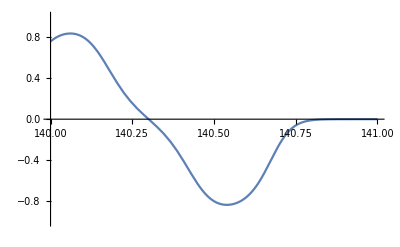

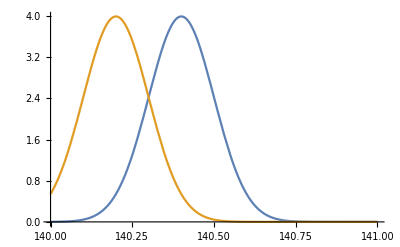

```mathematica
ClearAll["Global`*"];
(* The steady state function and some good values for Subscript[T, 1e] and Subscript[T, 1n] *)
physicalTimes={t1e->0.01,t1n->25*60};
pssn[a_,b_,c_]=(c t1n(b-a))/(t1e(2+a+b)+c t1n(a+b+2a b));
pssnPhysical[a_,b_,c_]=pssn[a,b,c]/.physicalTimes;

(* Try to model the steady state as a function of frequency *)
(* Here are a list of distributions to use in getting α,β in terms of frequency *)
gaussian[m_,s_,x_]=PDF[NormalDistribution[m,s],x];
cauchy[m_,s_,x_]=PDF[CauchyDistribution[m,s],x];
studentT2[m_,s_,x_]=PDF[StudentTDistribution[m,s,2],x];
studentT3[m_,s_,x_]=PDF[StudentTDistribution[m,s,3],x];
dist1[m_,s_,x_]=Exp[-Abs[(x-m)/s]];
dist21[m_,s_,x_]=gaussian[m-s,s,x]+gaussian[m+s,s,x];
dist22[m_,s_,x_]=gaussian[m-s,s/2,x]+gaussian[m+s,s/2,x];
constant[m_,s_,x_]=1;
(* Choose distribution here *)
distribution=gaussian;
(* Compute alpha, beta distributions *)
alphaDist[a_,m2_,s_,x_]=a distribution[m2,s,x];
betaDist[a_,m1_,s_,x_]=a distribution[m1,s,x];

(* Set up steady state function *)
pssnDistribution[a_,s_,m1_,m2_,c_,x_]=pssn[alphaDist[a,m2,s,x],betaDist[a,m1,s,x],c];
pssnDistributionPhysical[a_,s_,m1_,m2_,c_,x_]=pssnDistribution[a,s,m1,m2,c,x]/.physicalTimes;

testData={a->1,s->0.1,m1->140.2,m2->140.4,c->1*^-4};
Maximize[{pssnDistributionPhysical[a,s,m1,m2,c,x]/.testData,140≤x≤141},x]
Plot[pssnDistributionPhysical[a,s,m1,m2,c,x]/.testData,{x,140,141},PlotRange->{{140,141},{-1,1}}]
Plot[{alphaDist[a,m2,s,x]/.testData,betaDist[a,m1,s,x]/.testData},{x,140,141},PlotRange->All]
```

```mathematica
D[pssnDistribution[a,s,m1,m2,c,x],x]//FullSimplify
```

(2 a c ⅇ^(-((m1+m2) x)/s^2) √(2 π) t1n (a ⅇ^((m1^2+m2^2+2 x^2)/(2 s^2)) (m1-m2) √(2 π) s (t1e+c t1n)+a^2 c ⅇ^(x^2/(2 s^2)) t1n (ⅇ^((m1^2+2 m2 x)/(2 s^2)) (m1-x)+ⅇ^((m2^2+2 m1 x)/(2 s^2)) (-m2+x))+2 ⅇ^((m1^2+m2^2-2 (m1+m2) x+3 x^2)/(2 s^2)) π s^2 t1e (ⅇ^((m2^2+2 m1 x)/(2 s^2)) (m1-x)+ⅇ^((m1^2+2 m2 x)/(2 s^2)) (-m2+x))))/(s (4 ⅇ^((m1^2+m2^2-2 (m1+m2) x+2 x^2)/(2 s^2)) π s^2 t1e+2 a^2 c t1n+a ⅇ^((x (-2 (m1+m2)+x))/(2 s^2)) (ⅇ^((m2^2+2 m1 x)/(2 s^2))+ⅇ^((m1^2+2 m2 x)/(2 s^2))) √(2 π) s (t1e+c t1n))^2)